## Numerical calculations for orbits

We first have to initialise xAct, and set it up to use the Schwarzschild chart. We also constrain variables to remain in the region under the event horizon.

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->16,FontColor->Black};
```

```mathematica
<<xAct`xCoba`
<<xAct`ShowTime1`;
$RecursionLimit=Infinity;
Off[General::spell];
$DefInfoQ=False;
$CVVerbose=False;
$xCobaCacheVerbose=False;
$PrePrint=ScreenDollarIndices;
$Post=ScreenDollarIndices;
$CVSimplify=Together;
$CVReplace=False;
$CovDFormat="Postfix";
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M4,4,{μ,ν,α,β,σ}]
```

```mathematica
DefConstantSymbol[M]
```

```mathematica
DefChart[schw,M4, Range[0,3], {t[],r[],θ[],ϕ[]},FormatBasis->{"Partials","Differentials"},ChartColor->Red]
```

```mathematica
$Assumptions=And[
(t[]|r[]|θ[]|ϕ[])∈Reals,
2M>r[]>0,
0<=ϕ[],
M>0
];
```

```mathematica
gschw = CTensor[DiagonalMatrix[{-(1-(2M)/r[]),(1-(2M)/r[])^-1,r[]^2,(r[] Sin[θ[]])^2}],{-schw,-schw},0]
```

CTensor[{{-1+(2 M)/r,0,0,0},{0,1/(1-(2 M)/r),0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-schw,-schw},0]

```mathematica
SetCMetric[gschw,schw,SignatureOfMetric->{3,1,0}]
```

Having set up the chart, we go straight to computing the necessary geometric tensors needed for calculations (Riemann tensor, Ricci tensor, and the Christoffel symbols for the covariant derivative).

```mathematica
CDschw=CovDOfMetric[gschw]//FullSimplify;
```

```mathematica
MetricCompute[gschw,schw,All]//AbsoluteTiming
```

{0.048991,Null}

```mathematica
Christoffel[CDschw,PDschw][α,-β,-δ]//FullSimplify
```

0
M/(r (-2 M+r))
0
0 | M/(r (-2 M+r))
0
0
0 | 0
0
0
0 | 0
0
0
0
(M (-2 M+r))/r^3
0
0
0 | 0
M/(2 M r-r^2)
0
0 | 0
0
2 M-r
0 | 0
0
0
(2 M-r) Sin[θ]^2
0
0
0
0 | 0
0
1/r
0 | 0
1/r
0
0 | 0
0
0
-Cos[θ] Sin[θ]
0
0
0
0 | 0
0
0
1/r | 0
0
0
Cot[θ] | 0
1/r
Cot[θ]
0 | α |   |  
  | β | δ

```mathematica
Riemann[CDschw][-α,-β,-δ,σ]//FullSimplify
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (2 M (2 M-r))/r^4 | 0 | 0
-(2 M)/(r^2 (-2 M+r)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (M (-2 M+r))/r^4 | 0
0 | 0 | 0 | 0
M/r | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (M (-2 M+r))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(M Sin[θ]^2)/r | 0 | 0 | 0
0 | (2 M (-2 M+r))/r^4 | 0 | 0
(2 M)/(r^2 (-2 M+r)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | M/((2 M-r) r^2) | 0
0 | M/r | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | M/((2 M-r) r^2)
0 | 0 | 0 | 0
0 | (M Sin[θ]^2)/r | 0 | 0
0 | 0 | (M (2 M-r))/r^4 | 0
0 | 0 | 0 | 0
-M/r | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | M/(r^2 (-2 M+r)) | 0
0 | -M/r | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (2 M)/r
0 | 0 | -(2 M Sin[θ]^2)/r | 0
0 | 0 | 0 | (M (2 M-r))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | M/(r^2 (-2 M+r))
0 | 0 | 0 | 0
0 | -(M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(2 M)/r
0 | 0 | (2 M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 |   |   |   | σ
α | β | δ |

```mathematica
Ricci[CDschw][-α,-β]//FullSimplify
```

0

## Numerical calculations of geodesic equation

Now that we’re done with the charts, it’s time to create some curves. We’ll start with geodesics, and focus on purely radial infall first.

```mathematica
$Assumptions=And[$Assumptions,θ[]==π/2]
```

(t|r|θ|ϕ)∈ℝ&&2 M>r>0&&0≤ϕ&&M>0&&θ==π/2

```mathematica
DefParameter[λ]
DefParameter[τ]
DefConstantSymbol[amag]
DefScalarFunction/@{γt,γr,γϕ,at,ar,aϕ,e,L};
```

```mathematica
x={γt[λ],γr[λ],π/2,γϕ[λ]}
u=CTensor[D[x,λ],{schw},0]
a = CTensor[ {at[λ],ar[λ],0,aϕ[λ]},{schw},0]
```

{γt[λ],γr[λ],π/2,γϕ[λ]}

CTensor[{γt'[λ],γr'[λ],0,γϕ'[λ]},{schw},0]

CTensor[{at[λ],ar[λ],0,aϕ[λ]},{schw},0]

We can also define our functions representing individual constants.

```mathematica
constants=Flatten@{Solve[u[-ν]  CTensor[{0,0,0,1},{schw},0][ν]==L[λ],γϕ'[λ]],Solve[u[-ν] CTensor[{1,0,0,0},{schw},0][ν]==e[λ]//FullSimplify,γt'[λ]]}
```

{γϕ'[λ]→L[λ]/r^2,γt'[λ]→-(e[λ] r)/(-2 M+r)}

```mathematica
u[μ]/.constants//FullSimplify
```

(e[λ] r)/(2 M-r)
γr'[λ]
0
L[λ]/r^2 | μ

In any general relativity calculation, we have certain constants of motion. In this case, we have the normalisation of the 4-velocity; the normalisation of the 4-acceleration; and the orthogonality of the 4-velocity to 4-acceleration.

```mathematica
unorm=First@Simplify@Solve[u[α]u[-α]==-1,γr'[λ]]
anorm=Simplify@Solve[a[α] a[-α]==amag^2,at[λ]]
aunorm=First@Simplify@Solve[a[α] u[-α]==0,ar[λ]]
```

{γr'[λ]→-(√((2 M-r) (r+(2 M-r) γt'[λ]^2+r^3 γϕ'[λ]^2)))/r}

{{at[λ]→(√(r (ar[λ]^2 r+(2 M-r) (amag^2-aϕ[λ]^2 r^2))))/(-2 M+r)},{at[λ]→(√(r (ar[λ]^2 r+(2 M-r) (amag^2-aϕ[λ]^2 r^2))))/(2 M-r)}}

{ar[λ]→((2 M-r) (at[λ] (2 M-r) γt'[λ]+aϕ[λ] r^3 γϕ'[λ]))/(r^2 γr'[λ])}

```mathematica
Solve[First[(anorm/. aunorm/. unorm/. {at[λ]->0,γt'[λ]->0}//FullSimplify)/. {Rule->Equal}],aϕ[λ]]
```

{{aϕ[λ]→-(amag √(1+r^2 γϕ'[λ]^2))/r},{aϕ[λ]→(amag √(1+r^2 γϕ'[λ]^2))/r}}

```mathematica
unorm/.constants//Simplify
```

{γr'[λ]→-(√(L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r)))/r}

But the important part is played by the equations of motion:

```mathematica
eqOfMotion=ParamD[λ][u[α]]+Christoffel[CDschw,PDschw][α,-β,-δ] u[β] u[δ]-a[α]
```

●
●
-Cos[θ] Sin[θ] γϕ'[λ]^2
-aϕ[λ]+(2 γr'[λ] γϕ'[λ])/r+γϕ''[λ] | α

## Auxiliary functions for display and calculation

We will need functions for display of our graphs:

```mathematica
DisplayCartesianTPlots[plots_,labels_:{},positive_:False,M_:1]:=Module[{},
Show[
Plot[
{0},
{r,0,2M},
PlotRange->{{0,2.05M},{If[positive,-1,-25],25}},
PlotStyle->None,
GridLines->{{{1M,Directive[Gray,Thin,Dashed]},{2M,Directive[Black,Thick]}},ResourceFunction["CartesianProduct"][Range[If[positive,0,-20],20,10],{Directive[Gray,Thin,Dashed]}]},
Axes->{True,True},
AxesLabel->{MaTeX["r",Magnification->1.1], MaTeX["t",Magnification->1.1]},
AxesStyle->{Directive[Thickness[-2]],Directive[Black,Thick]},
AxesOrigin->{0,If[positive,0,-25]},
BaseStyle->texStyle,
LabelStyle->texStyle,
Ticks->{{{1M,MaTeX["1M",Magnification->1.1]},{2M,MaTeX["2M",Magnification->1.1]}},({#,MaTeX[#,Magnification->1.1]})&/@Range[If[positive,0,-20],20,10]}],
plots,
labels,
PlotRange->{{0,2.05M},{If[positive,-1,-25],25}},
PlotLabels->Automatic,
LabelStyle->texStyle,
ImageSize->Large,
TicksStyle->texStyle
]
]
Options[colorPolarAxes]={PolarAxesStyle->{},PolarLabelsStyle->{},PolarTicksStyle->{}};
colorPolarAxes[plot_Graphics,OptionsPattern[]]:=ReplaceAll[plot,{Text[Style[lbl__,{}],pos__]:>Text[Style[lbl,OptionValue[PolarLabelsStyle]],pos],Style[Line[def__],{}]:>Style[Line[def],OptionValue[PolarTicksStyle]],Circle[options__]:>Style[Circle[options],OptionValue[PolarAxesStyle]]}]
DisplayPolarPhiPlots[plots_,labels_:{},M_:1]:=Module[{},
Show[
colorPolarAxes[PolarPlot[
{2},
{r,0,2M},
PlotStyle->None,
PolarGridLines->{
ResourceFunction["CartesianProduct"][Range[0,2π,π/6],{Directive[Gray,Thick,Dashed]}],{{1M,Directive[Gray,Thick,Dashed]},{2M,Directive[Black,Thick]}}
},
PolarAxes->True,
PolarAxesOrigin->{0,2M},
PolarTicks->{({#,MaTeX[#,Magnification->1.1]})&/@Range[0,2 π-π/6,π/6],{{1M,MaTeX["1M",Magnification->1.1]},{2M,MaTeX["2M",Magnification->1.1]}}},
PlotRangeClipping->False,
PlotRangePadding->.1,
LabelStyle->texStyle,
BaseStyle->texStyle
],
PolarLabelsStyle->texStyle],
plots,
labels,
PlotRange->Automatic,
ImageSize->Large
]
]
```

But we really are interested in solving equations up to the best geodesic using numerical calculation:

```mathematica
solveEquationsUpToBestGeodesic[eqs_,u_,a_,unorm_,aeqs_,constants_,γstart_List,ustartConstants_List,amagnitude_,mass_,λrange_List,assumptions_,plotfunc_:γt,debug_:False]:=Block[
{$Assumptions=And[$Assumptions,assumptions,θ[]==π/2],eqTable,ustart,system,solution,root,rootVals,solutionFall,solutionCombined,constantEqs},
eqTable =  Table[(Simplify@eqs)[[0]][{i,schw}]==0,{i,0,3}];
ustart=Flatten@{constants/.r[]->γr[λ]/.λ->0/.ustartConstants/.γstart,Simplify[unorm/.constants/.r[]->γr[λ]]/.λ->0/.ustartConstants/.γstart};
system=Join[Select[eqTable,Not[TrueQ[#]]&]/.aeqs/.r[]->γr[λ]//Simplify,γstart,ustart]/.Rule->Equal;
solution=NDSolve[system/.{M->mass,amag->amagnitude},{γt,γr,γϕ},Join[{λ},λrange]];
root=Re@First@Values@FindRoot[plotfunc'[λ]/.solution,{λ,0}];
rootVals={γt[root]==N[γt[root]/.solution][[1]],γr[root]==N[γr[root]/.solution][[1]],γϕ[root]==N[γϕ[root]/.solution][[1]],plotfunc'[root]==0,γr'[root]==N[γr'[root]/.solution][[1]]};
solutionFall=NDSolve[Join[Select[eqTable,Not[TrueQ[#]]&]/.aeqs/.r[]->γr[λ]//Simplify,rootVals]/.Rule->Equal/.{M->mass,amag->0},{γt,γr,γϕ},Join[{λ,root},{λrange[[2]]}]];
solutionCombined=
{
γt->Function[Piecewise[{{γt[#]/.solution,# <= root},{γt[#]/.solutionFall, # > root}}]],
γr->Function[Piecewise[{{γr[#]/.solution,# <= root},{γr[#]/.solutionFall, # > root}}]],
γϕ->Function[Piecewise[{{γϕ[#]/.solution,# <= root},{γϕ[#]/.solutionFall, # > root}}]]
};
constantEqs=(Solve[constants/.Rule->Equal,{e[λ],L[λ]}]/.r[]->γr[λ]//Simplify);
If[debug,
Print[Simplify/@{unorm,constants,eqs}];
Print[Simplify@(eqTable/.unorm)/.r[]->γr[λ]/.M->mass];
Print[ustart];
Print[aeqs];
Print[system//Simplify];
Print[solution];
Print[root];
Print[rootVals];
Print[solutionFall];
Print[solutionCombined];
Print[constantEqs];
];
Return[{ParametricPlot[{γr[λ],plotfunc[λ]}/.solutionCombined,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solutionFall]},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->0.5,Exclusions->None,BaseStyle->texStyle],
ParametricPlot[{γr[λ] * Cos[plotfunc[λ]],γr[λ] * Sin[plotfunc[λ]]}/.solutionCombined,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solutionFall]},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->1,Exclusions->None,BaseStyle->texStyle],
ParametricPlot3D[{γr[λ]*Cos[γϕ[λ]],γr[λ]*Sin[γϕ[λ]],γt[λ]}/.solutionCombined,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solutionFall]},ColorFunction->Function[{x,y,z,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],BoxRatios->{1,1,1},Exclusions->None,BaseStyle->texStyle],
system,
ParametricPlot[({{γr[λ],e[λ]},{γr[λ],L[λ]}(*+(rstar[γr[λ]]/.M->mass)-γr[λ]*)}/.constantEqs[[1]]//Simplify)/.solutionCombined/.M->mass,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solutionFall]},Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->0.5,Exclusions->None,PlotStyle->{Blue,Orange},Evaluated->True,BaseStyle->texStyle]
}]
];
```

NDSolve::ndsz: At λ == 3.13544, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 3.10107, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.13344} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.13152} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.12938} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

3.42989

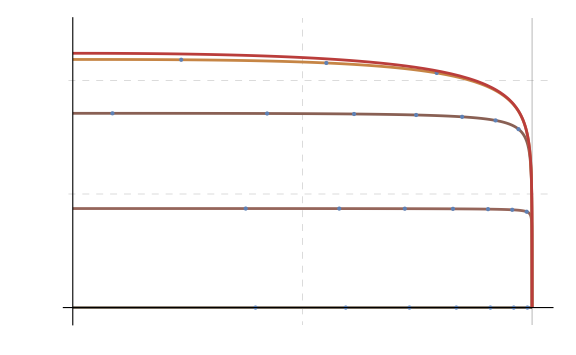

```mathematica
DisplayCartesianTPlots[Table[solveEquationsUpToBestGeodesic[eqOfMotion,u,a,unorm,{},constants[[2]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->eval,L[0]->0},0,1,{0,π},And[γϕ'[λ]==γϕ''[λ]==0,aϕ[λ]==ar[λ]==at[λ]==0,L[λ]==0]][[1]],{eval,{0,0.01,0.1,1,10}}],{},True]
```